## Config and data

```mathematica
(*MaTeX used for aesthetics*)
<<MaTeX`
$Assumptions={{E0,lam,n1,rho,R}>0};
```

### Settings

```mathematica
(*Units*)
$Assumptions={eV>0, meter>0,kg>0,sec>0,α>0,λ>0,0<as<1,fa>0,μa>0};
GN= (6.71 10^-39 GeV^-2);Mpl=1/√GN;
GeV=10^9 eV;
meter=5.0677 10^6 1/eV;
kg=1/(1.783*10^−27)GeV;sec=1.52 10^15 1/eV ;hbar= 6.5821*10^-25 GeV sec; c= 3*10^8 meter/sec; year  = 3.15569*10^7 sec; day=24*60^2 sec;msec = 10^-3 sec; cm = 10^-2 meter; 
 km = 10^3 meter; nm = 10^-9 meter; MeV = 10^6 eV; Hz = 1/sec; THz = 10^12 Hz;Volt = eV/e; Kelvin = 8.6173*10^-5 eV; Tesla=195.353 eV^2; Liter=(10cm)^3; mm = 10^-3meter; kHz = 10^3 Hz;
erg=6.2415*10^11 eV; micro = 10^-6; μm = 10^-6 meter; Joule = 6.242*10^18eV; AU =1.496*10^11 meter;
Tuni=4.354*10^17 sec;Msun=1.1 10^57 GeV ;Mpc =3.086*10^22 meter/(c hbar);
kpc=Mpc/1000;
inch = 2.56cm; 

(*useful functions and colors*)
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)] (*python logspace*)
sv2[a_] := a /. {nm -> 0.005067730926738493, eV -> 1};
tfn[t_,x_,y_] := Text[Style[t,14, FontFamily ->" Arial"],{Log[x],y Log[10]}]
tfn2[t_,x_,y_] := Text[Style[t,13, FontFamily ->" Arial"],{x,y}];
fst[a_] := a[[1]]; snd[a_] := a[[2]];
Zip[a___] := Transpose[{a}]
Eqlen[l_] := With[{lmin = Min[Length /@ l]}, Take[#, lmin] & /@ l]
ilist[l_] := Range[Length[l]]
fn[rule_] := Replace[#, rule] &
importCSV[s_] := ImportString[s,"CSV"];
RGBColor256[R_,G_,B_]:=RGBColor[R/256,G/256,B/256];
colList1 =Partition[RGBColor256@@# &/@ {{2,63,165},{125,135,185},{190,193,212},{214,188,192},{187,119,132},{142,6,59},{74,111,227},{133,149,225},{181,187,227},{230,175,185},{224,123,145},{211,63,106},{17,198,56},{141,213,147},{198,222,199},{234,211,198},{240,185,141},{239,151,8},{15,207,192},{156,222,214},{213,234,231},{243,225,235},{246,196,225},{247,156,212}},6];
RGBColor256[R_,G_,B_]:=RGBColor[R/256,G/256,B/256];
lightsteelblue2=RGBColor[188/256,210/256,238/256];
steelblue2=RGBColor[92/256,172/256,238/256];
cornflowerblue=RGBColor[100/256,149/256,237/256];
aquamarine3=RGBColor256[102,205,170];
lightcyan2 = RGBColor256[209,238,238];
lightcyan3 = RGBColor256[195,220,220];
lightcyan4=RGBColor256[122,139,139];
lavender=RGBColor256[230,230,250];
nicegreen=RGBColor256[46, 139 ,87];
nicered=RGBColor[0.7,0.02,0.337];
niceblue=RGBColor256[113,113,198];
niceorange=RGBColor256[238, 121, 66];
mmacolors=ColorData[97,"ColorList"];

(*Plot settings*)
plotstyle={PlotRange->All,Background->White,ImageSize->500,GridLines->Automatic,LabelStyle-> {Black,14,FontFamily->"Arial"},Frame->True,GridLinesStyle->Directive[Lighter[Gray,0.8],Thickness[0.001],Dashed],FrameStyle->Directive[Black,Thickness[0.001]],Axes->False,AspectRatio->1/1.2(*GoldenRatio^-1*)};
SetOptions[{LogPlot,LogLogPlot,LogLinearPlot,Plot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot},BaseStyle->{FontSize->16},ImageSize->550,Frame->True,PlotStyle->Thick,AspectRatio->1/GoldenRatio];
SetOptions[{ContourPlot,DensityPlot,RegionPlot},BaseStyle->{FontSize->16},ImageSize->550,Frame->True,AspectRatio->1/GoldenRatio];
SetOptions[LineLegend,LabelStyle->{FontSize->14}];
SetOptions[SwatchLegend,LabelStyle->{FontSize->14}];
SetDirectory[NotebookDirectory[]];
(*colors*)
RGBColor256[R_,G_,B_]:=RGBColor[R/256,G/256,B/256];
lightsteelblue2=RGBColor256[188,210,238];
steelblue2=RGBColor256[92,172,238];
lightsteelblue2=RGBColor256[188,210,238];
cornflowerblue=RGBColor256[100,149,237];
aquamarine3=RGBColor256[102,205,170];
lightcyan2 = RGBColor256[209,238,238];
lightcyan3 = RGBColor256[195,220,220];
lightcyan4=RGBColor256[122,139,139];
lavender=RGBColor256[230,230,250];
nicegreen=RGBColor256[46, 139 ,87];
nicered=RGBColor[0.7,0.02,0.337];
niceblue=RGBColor256[113,113,198];
niceorange=RGBColor256[238, 121, 66];
```

### dphase data

```mathematica
(*import data*)
SetDirectory[NotebookDirectory[]];
(*changing standard deviation*)
fill5s5=ArrayFlatten[Import["Figure5(a)\\ff_0p5_std_0p5_noloss.csv"],1];
fill5s4=ArrayFlatten[Import["Figure5(a)\\ff_0p5_std_0p4_noloss.csv"],1];
fill5s3=ArrayFlatten[Import["Figure5(a)\\ff_0p5_std_0p3_noloss.csv"],1];
fill5s2=ArrayFlatten[Import["Figure5(a)\\ff_0p5_std_0p2_noloss.csv"],1];
fill5s1=ArrayFlatten[Import["Figure5(a)\\ff_0p5_std_0p1_noloss.csv"],1];
(*changing filling factor*)
fill4s5=ArrayFlatten[Import["Figure5(c)\\ff_0p4_std_0p5_noloss.csv"],1];
fill3s5=ArrayFlatten[Import["Figure5(c)\\ff_0p3_std_0p5_noloss.csv"],1];
fill2s5=ArrayFlatten[Import["Figure5(c)\\ff_0p2_std_0p5_noloss.csv"],1];
fill1s5=ArrayFlatten[Import["Figure5(c)\\ff_0p1_std_0p5_noloss.csv"],1];
(*changing loss*)
loss0p1=ArrayFlatten[Import["Figure5(b)\\ff_0p5_std_0p5_loss_0p1.csv"],1];
loss0p3=ArrayFlatten[Import["Figure5(b)\\ff_0p5_std_0p5_loss_0p3.csv"],1];
loss1=ArrayFlatten[Import["Figure5(b)\\ff_0p5_std_0p5_loss_1.csv"],1];
```

### Data for experiments

```mathematica
(*DP searches*)
QC={{0.61227643 10^-3, 4 10^-11},{0.6122764310^-3, 4 10^-11}};
haloscope=Import["axion limit data\\haloscopes.txt","Data"];
sensei1=Import["axion limit data\\dp_sensei.txt","Data"];
damic=Import["axion limit data\\dp_damic.txt","Data"];
darkside=Import["axion limit data\\dp_darkside.txt","Data"];
cdms=Import["axion limit data\\dp_supercdms.txt","Data"];
jwst=Import["axion limit data\\dp_jwst.txt","Data"];
xenonSolar=Import["axion limit data\\XENON1T_Solar_S2.txt","Data"];
xenon1TSE=Import["axion limit data\\XENON1T_SE.txt","Data"];
xenonerratum=Import["axion limit data\\XENON1T_Solar_SE.txt","Data"];
damicM=Import["axion limit data\\dp_damic_m.txt","Data"];
jwstsaha=Import["axion limit data\\axion_JWST_Saha.txt","Data"];
jwstpinetti=Import["axion limit data\\axion_JWST_Pinetti.txt","Data"];
desi=Import["axion limit data\\axion_desi.txt","Data"];
```

```mathematica
Xenon={{-4.606676343,-6.962599898},{-1.863570392,-9.682058156},{-1.123367199,-10.44195939},{-0.368650218,-11.18179511},{0.269956459,-11.92186348},{0.908563135,-12.76211399},{1.387518142,-13.00159149},{1.880986938,-13.26107635},{2.316400581,-13.13998535}};
Solar={{-4.558766859344889,-6.811550151975686},{-4.050096339113672,-7.340425531914897},{0.2967244701348797,-11.662613981762917},{0.6358381502890254,-12.009118541033436},{0.7591522157996238,-12.173252279635257},{0.9903660886319905,-12.902735562310031},{1.1907514450867147,-13.285714285714288},{1.437379576107908,-13.632218844984802},{2.2235067437379676,-14.580547112462005},{2.3314065510597395,-14.708206686930092},{2.439306358381515,-14.617021276595747},{2.470134874759161,-13.632218844984802},{2.5163776493256336,-13.340425531914894},{2.732177263969181,-13.030395136778116},{3.102119460500969,-12.775075987841944},{3.348747591522166,-12.519756838905774},{3.54913294797689,-12.264437689969604},{3.7186897880539576,-11.91793313069909},{3.903660886319855,-11.480243161094226},{4.119460500963399,-10.732522796352585},{4.211946050096344,-10.167173252279637},{4.335260115606946,-9.474164133738602},{4.489402697495194,-8.01519756838906},{4.55105973025049,-7.212765957446811},{4.705202312138738,-4.62310030395137}};
HBStar={{2.470134874759154,-13.996960486322186},{2.639691714836225,-14.14285714285714},{2.8554913294797792,-14.39817629179331},{3.0404624277456733,-14.598784194528875},{3.210019267822748,-14.79939209726444},{3.3641618497109924,-14.963525835866262},{3.425818882466288,-14.325227963525835},{3.4566473988439377,-13.595744680851062},{3.564547206165713,-13.468085106382977},{3.749518304431607,-13.340425531914894},{4.0578034682081,-13.267477203647417},{4.304431599229293,-13.194528875379943},{4.504816955684017,-13.048632218844984},{4.7360308285163875,-12.647416413373861},{4.8901734104046355,-12.246200607902736},{5.075144508670526,-11.443768996960488},{5.1984585741811244,-10.6048632218845},{5.3063583815029,-9.802431610942252},{5.3680154142581955,-9.109422492401217}};
XenonDM={{1.064660116,-12.0066335},{1.064528106,-12.05970149},{1.064379595,-12.11940299},{1.064231083,-12.17910448},{1.064082572,-12.23880597},{1.063934061,-12.29850746},{1.063736046,-12.37810945},{1.063538031,-12.45771144},{1.063340016,-12.53731343},{1.063092498,-12.63681592},{1.06286148,-12.72968491},{1.062646964,-12.8159204},{1.062498453,-12.87562189},{1.062283937,-12.96185738},{1.062085922,-13.04145937},{1.061838403,-13.14096186},{1.061623887,-13.22719735},{1.061409371,-13.31343284},{1.061178354,-13.40630182},{1.060897833,-13.51907131},{1.060617311,-13.6318408},{1.060386294,-13.72470978},{1.070072523,-13.83084577},{1.069775501,-13.95024876},{1.069494979,-14.06301824},{1.079164707,-14.17578773},{1.08890044,-14.26202322},{1.093578542,-14.3814262},{1.088751929,-14.32172471},{1.09833915,-14.46766169},{1.10804188,-14.56716418},{1.122769238,-14.64676617},{1.147479848,-14.71310116},{1.172173956,-14.78606965},{1.206851316,-14.84577114},{1.236611305,-14.88225539},{1.271445426,-14.87893864},{1.296387053,-14.85240464},{1.326336807,-14.81260365},{1.341328185,-14.78606965},{1.356327814,-14.75621891},{1.366352318,-14.72636816},{1.386384825,-14.67330017},{1.406466837,-14.60033167},{1.41142546,-14.60696517},{1.431507471,-14.53399668},{1.46658086,-14.4344942},{1.451523477,-14.48756219},{1.486613368,-14.3814262},{1.506662376,-14.32172471},{1.531752514,-14.23548922},{1.551834526,-14.16252073},{1.571875284,-14.10613599},{1.596915918,-14.039801},{1.626939927,-13.97014925},{1.651931058,-13.92371476},{1.681889062,-13.88059701},{1.716797439,-13.84742952},{1.756656188,-13.82421227},{1.786498684,-13.82752902},{1.791300545,-13.89718076},{1.796110657,-13.96351575},{1.800920769,-14.02985075},{1.810722507,-14.08955224},{1.820524244,-14.14925373},{1.850490499,-14.10281924},{1.865292113,-14.15257048},{1.815615125,-14.12271973},{1.88012673,-14.18905473},{1.889994472,-14.22222222},{1.899862215,-14.25538972},{1.919680206,-14.28855721},{1.939498197,-14.32172471},{1.964299564,-14.35157546},{2.004100559,-14.35157546},{2.02405056,-14.33167496},{2.044025313,-14.30182421},{2.059033192,-14.26865672},{2.074065823,-14.22553897},{2.089131457,-14.16915423},{2.104213592,-14.10613599},{2.124320355,-14.02321725},{2.134402614,-13.97014925},{2.149476498,-13.91044776},{2.159575258,-13.85074627},{2.169674018,-13.79104478},{2.184731401,-13.73797678},{2.19481366,-13.68490879},{2.204895918,-13.6318408},{2.214978177,-13.5787728},{2.23999406,-13.52238806},{2.245026938,-13.49917081},{2.284877437,-13.47927032},{2.344529426,-13.49917081},{2.394222915,-13.52238806},{2.443974159,-13.52238806},{2.483832908,-13.49917081},{2.518724784,-13.47263682},{2.568575035,-13.43283582},{2.603491663,-13.39635158},{2.63840004,-13.36318408},{2.678308293,-13.32006633},{2.713249672,-13.27363184},{2.763149427,-13.21393035},{2.788107555,-13.18076285},{2.818049058,-13.14427861},{2.827826044,-13.21393035},{2.827669282,-13.27694859},{2.832504146,-13.33333333},{2.83734726,-13.38640133},{2.842198625,-13.43615257},{2.852025115,-13.48590381},{2.876991494,-13.44941957},{2.901966123,-13.40961857},{2.926957254,-13.36318408},{2.946932007,-13.33333333},{2.976848758,-13.30679934},{2.996782258,-13.29353234}};
```

```mathematica
xenondm=Table[{XenonDM[[i,1]],10^XenonDM[[i,2]]},{i,1,Length[XenonDM]}];
xenon=Table[{Xenon[[i,1]],10^Xenon[[i,2]]},{i,1,Length[Xenon]}];
solar=Table[{Solar[[i,1]],10^Solar[[i,2]]},{i,1,Length[Solar]}];
```

```mathematica
funkraw1 = importCSV["1.9441852228961005, -10.650759219088936
1.977387223870026, -10.919739696312364
2.0022665899331535, -11.11062906724512
2.043490194342379, -11.310195227765727
2.0928062331223165, -11.475054229934923
2.1830625525698357, -11.700650759219089
2.281305059984949, -11.839479392624728
2.4530612244897974, -12
2.918615255212715, -12.121475054229935
3.1635928991987257, -12.16052060737527
3.3595378281464434, -12.173535791757049
3.792155473903227, -12.156182212581344
4.983753154190093, -12.039045553145336
5.457187126477489, -12.02169197396963
5.653105493824428, -12.02169197396963
6.012324582761522, -12.039045553145336
6.200079684802338, -12.039045553145336
6.616353092213024, -12.013015184381779
6.877497897206606, -11.973969631236443
7.122307317721016, -11.93058568329718
7.530302359555541, -11.84815618221258
7.628164150692817, -11.800433839479393
7.734251184204701, -11.783080260303688
7.8728584709371825, -11.700650759219089
8.019726415511975, -11.665943600867678
8.16654123688521, -11.605206073752711
8.272522023993982, -11.535791757049891
8.353977599716679, -11.449023861171366
8.419071229359425, -11.344902386117136
8.54922307317721, -11.119305856832971"];
funk1 = fn[{a_,b_}:> {a,10^b}] /@ funkraw1;
LAMPOST2022={{0.8377310356839152,4.660442573466144*^-11},{0.8349103924661243,4.38645267391349*^-11},{0.8321086797397278,4.0604769019193544*^-11},{0.8293257075666851,3.868278905536553*^-11},{0.8265612885414628,3.721651300566591*^-11},{0.8238152377489664,1.6892048770093165*^-11},{0.8210873727233076,1.0055668853490173*^-11},{0.8183775134073891,6.954884748922167*^-12},{0.8156854821132858,5.251217424655281*^-12},{0.8130111034834062,4.203273540653735*^-12},{0.8103542044524147,3.480333453269754*^-12},{0.8077146142098985,3.001995647806075*^-12},{0.8050921641637627,2.660822622184138*^-12},{0.802486687904333,2.38859461729731*^-12},{0.7998980211691578,2.2282307287923562*^-12},{0.7973260018084852,2.089086791607574*^-12},{0.7947704697514066,2.0020404362586003*^-12},{0.7922312669726481,1.9576046425096456*^-12},{0.7897082374599964,1.908284245651621*^-12},{0.7872012271823456,1.870106806568891*^-12},{0.784710084058351,1.826072157092303*^-12},{0.7822346579256747,1.7895610001794112*^-12},{0.779774800510814,1.756255289569216*^-12},{0.7773303653994948,1.7222153200027364*^-12},{0.7749012080076215,1.687372308937636*^-12},{0.7724871855527691,1.6515138258817886*^-12},{0.7700881570262077,1.6171568366039473*^-12},{0.7677039831654455,1.5821390297175322*^-12},{0.7653345264272805,1.557035237230789*^-12},{0.7629796509613503,1.5250510560624169*^-12},{0.7606392225841683,1.4896764709690087*^-12},{0.7583131087536357,1.4512445773809487*^-12},{0.7560011785440209,1.4083538187864233*^-12},{0.7537033026213947,1.3672528350012096*^-12},{0.7514193532195118,1.325452341259311*^-12},{0.7491492041161295,1.2794555135072056*^-12},{0.7468927306097557,1.2297457614997541*^-12},{0.7446498094968135,1.1775195108822336*^-12},{0.7424203190492182,1.123968501635892*^-12},{0.7402041389923549,1.0695100233954305*^-12},{0.738001150483449,1.0118884227499958*^-12},{0.7358112360903231,9.587611432045236*^-13},{0.7336342797705293,9.06411872597514*^-13},{0.7314701668508522,8.537958195216294*^-13},{0.7293187840071732,8.087175359026957*^-13},{0.7271800192446888,8.445569193191897*^-13},{0.7250537618784763,9.585942422577097*^-13},{0.7229399025143991,1.1137210489626414*^-12},{0.7208383330303456,1.301888874624135*^-12},{0.7187489465577939,1.5178875611497948*^-12},{0.7166716374636962,1.7769732039395067*^-12},{0.7146063013326769,2.0833195437805475*^-12},{0.712552834949537,2.451310848916306*^-12},{0.7105111362820599,2.8427414612763794*^-12},{0.7084811044641112,3.315140272895297*^-12},{0.7064626397790282,3.872743443473756*^-12},{0.7044556436432923,4.606400883942589*^-12},{0.7024600185904785,5.549682411110347*^-12},{0.700475668255477,6.665690018723258*^-12},{0.6985024973589827,7.800599301383765*^-12},{0.696540411692244,9.998580182934155*^-12},{0.6945893181020697,1.3464456790323083*^-11},{0.6926491244760862,1.8330354517174222*^-11},{0.6907197397282421,2.3093668457336395*^-11}};
xenon10 = {{12.275304049726874,5.569335198445787*^-13},{12.275304049726874,3.62037033446633*^-15},{12.275304049726874,1.7660475723974079*^-15},{12.275304049726874,1.4160517879394427*^-15},{12.570566177135252,1.0167033267314924*^-15},{12.720849924977966,6.536536969603815*^-16},{13.026828921186654,6.117454437124791*^-16},{13.340167735856598,6.682516626209733*^-16},{13.661043397242866,7.380835321023529*^-16},{15.023606277481631,1.1106150367993903*^-15},{15.755034366496549,1.4082541999990305*^-15},{16.522072217876037,1.805488490327979*^-15},{17.326453501949032,2.227008232830292*^-15},{18.387222399253506,2.8082854316100412*^-15},{19.168169679299574,3.223987025459721*^-15},{20.221177975221742,3.660573746738379*^-15},{21.459169157927455,4.225706024204151*^-15},{24.02399126536595,5.328668520887132*^-15},{24.456094100730745,4.179295867440355*^-15},{25.64674525615127,4.465602845956932*^-15},{26.26363527653333,3.62037033446633*^-15},{29.577927626011046,4.465602845956932*^-15},{32.14376721029517,5.387842206895665*^-15},{36.200092263044525,7.340192236512413*^-15},{38.8756281464034,8.662632293328602*^-15},{40.286662504351554,5.820871467434239*^-15},{45.370565624323135,6.945869487863138*^-15},{48.7238879168215,7.42170344873046*^-15},{52.95061001506823,7.671708387550647*^-15},{54.22424932349484,5.631181434708596*^-15},{59.63261727816489,5.693714459753857*^-15},{61.430930939347036,5.447673003606827*^-15},{62.535846402593094,4.987027081565481*^-15},{63.28347552601262,4.179295867440355*^-15},{64.04004271197283,3.2778383341240535*^-15},{65.58041997463478,2.5425867495542853*^-15},{67.1578484635426,1.8458102373095448*^-15},{70.42744538034077,2.0163055935152192*^-15},{73.85622345381542,1.6346668541270069*^-15},{76.53691760103719,1.4317767300226107*^-15},{80.26313688195168,1.2540687415657139*^-15},{81.22269947080099,1.0279935924299534*^-15},{84.17076809536437,9.30732630422325*^-16},{91.47245235632514,8.905130491118558*^-16},{95.92581194181818,8.710597807724144*^-16},{95.92581194181818,7.886467065393163*^-16},{103.01565442414451,8.426737634474961*^-16},{108.03099773535817,8.905130491118558*^-16},{109.32253090849302,1.0167033267314924*^-15},{113.2905143100425,1.1106150367993903*^-15},{121.66377573927201,1.4317767300226107*^-15},{129.112336936076,1.5813964785845016*^-15},{135.3982038663718,2.061335492301485*^-15},{145.4054367307101,2.8082854316100412*^-15},{154.30752190154786,3.660573746738379*^-15},{163.75461503199625,4.6672895892813046*^-15},{175.85766011265733,5.387842206895665*^-15},{191.1130407878005,5.569335198445764*^-15},{205.2381373397667,5.447673003606827*^-15},{206.46132476544287,4.4165579462552904*^-15},{217.80333036130696,4.272631555499707*^-15},{223.0422290817456,4.771523579648371*^-15},{242.39079831151273,4.565332591695785*^-15},{260.3058155983748,4.565332591695785*^-15},{263.4178260680809,4.087999098616658*^-15},{287.97503432175785,4.1333954249440695*^-15},{291.41783608845395,5.15501835325051*^-15},{300.2059909552016,5.1835619989530465*^-15},{303.79501636661433,4.824510294242774*^-15},{326.24839746764087,5.042406914911068*^-15},{330.14876529580613,4.616029600948023*^-15},{346.22214182277867,4.719118808453872*^-15},{350.36129994231504,5.270144728654506*^-15},{358.78866128208074,6.429148796648021*^-15},{389.9130240552279,6.945869487863138*^-15},{399.2917366737025,8.107237610134029*^-15},{408.89603870559284,8.56749218646416*^-15},{433.92967874284034,8.107237610134029*^-15},{439.117398810714,9.154417084622483*^-15},{455.0556554110026,9.890171828097012*^-15},{477.2101556212207,1.0685060324987102*^-14},{494.53103138964644,1.1672026985678669*^-14},{512.4805876960936,1.0685060324987102*^-14},{537.4308353258955,1.1417051414861301*^-14},{550.3578448020241,1.2199188310127187*^-14},{563.5957921012395,1.261012595378243*^-14},{570.3336976746123,1.2199188310127187*^-14},{598.1005386637972,1.2750158614998323*^-14},{627.2192153619053,1.1801642265222965*^-14},{649.9848375534754,1.4397045636221093*^-14},{681.6295145264733,1.504728107990609*^-14},{681.6295145264733,6.1174544371247906*^-15},{698.0249846303602,6.645718882299559*^-15},{740.7598231911801,7.100990716027665*^-15},{758.5775750291851,7.756901013343474*^-15},{786.1109956469628,8.288295526252827*^-15},{824.3830092154674,8.856093768933182*^-15},{834.2386805143562,9.56787180339626*^-15},{885.3128628401529,9.25607486273971*^-15},{973.6146425232006,9.358861528011217*^-15}};
sunCoolingRaw2 = importCSV["-1.7906345709526628, -10.03136585890065
-1.7295595794601764, -10.089767534267203
-1.6745920871169382, -10.144904679364586
-1.6196245947737005, -10.20004182446197
-1.5646571024304627, -10.255178969559354
-1.5096896100872246, -10.31059886924698
-1.4516683681693627, -10.36912906942728
-1.3905933766768763, -10.430204060919767
-1.3295183851843895, -10.491279052412253
-1.268443393691903, -10.551845085642302
-1.2104221517740408, -10.610318734904553
-1.155454659430803, -10.666304143772667
-1.1004871670875653, -10.720310270509078
-1.0455196747443272, -10.774599151835732
-0.9905521824010894, -10.82917078775263
-0.9355846900578517, -10.885156196620743
-0.880617197714614, -10.940010587127883
-0.8256497053713758, -10.995995995995996
-0.7706822130281381, -11.049719368142165
-0.7157147206849004, -11.10400824946882
-0.6607472283416622, -11.160276412927175
-0.6057797359984245, -11.21456529425383
-0.5508122436551868, -11.269136930170728
-0.4958447513119486, -11.323708566087625
-0.4408772589687109, -11.37997672954598
-0.38590976662547316, -11.434548365462877
-0.33094227428223544, -11.487988983018804
-0.2759747819389977, -11.54425714647716
-0.2210072895957591, -11.598828782394058
-0.16603979725252138, -11.653965927491441
-0.11107230490928366, -11.709103072588825
-0.056104812566045936, -11.76452297227645
-0.0011373202228082135, -11.81909460819335
0.05383017212042951, -11.87394899870049
0.10879766446366723, -11.929934407568602
0.16681890638152996, -11.987616343978173
0.2248401482993918, -12.045581034977987
0.27980764064262953, -12.101000934665613
0.33477513298586725, -12.155855325172753
0.38668887575448085, -12.207104594654297
0.4381727652105383, -12.26169085397051
0.4813551125678357, -12.30373597586984
0.5363226049110734, -12.359721384737952
0.5912900972543111, -12.41771300474636
0.6432038400229247, -12.473671484605878
0.6920638332169133, -12.529656893473991
0.7378700768362787, -12.587823552038264
0.780622570881019, -12.64344541929035
0.8203213153511353, -12.701854438931974
0.8539125606720033, -12.75359852894644
0.8793604737938718, -12.810856333470648
0.8992825543521361, -12.86302455537048
0.9210950513137384, -12.923145250120896
0.9429075482753406, -12.981539122195185
0.9669012949331028, -13.040841848309542
0.9908950415908659, -13.098963064171812
1.0127075385524682, -13.158220347584164
1.0345200355140705, -13.215296381300357
1.0585137821718327, -13.270191165320389
1.0853189173268687, -13.330417893042148
1.1104275249404463, -13.384261435889169
1.134857521537441, -13.440310464540087
1.1566700184990433, -13.49304217594476
1.1806637651568055, -13.548209616176813
1.2046575118145686, -13.606467160145092
1.2238525091407784, -13.665360901941419
1.2478462557985406, -13.728889799342085
1.277162251714934, -13.79619952954943
1.3364049934626463, -13.838373661932309
1.3944262353805081, -13.794418175630899
1.4524474772983709, -13.747455208687812
1.519629967940106, -13.733111839473668
1.586812458581841, -13.736582009444831
1.6539949492235761, -13.748149242682045
1.7211774398653112, -13.76573143720261
1.7883599305070463, -13.789791282336013
1.8555424211487814, -13.81778398677007
1.9227249117905165, -13.844157278550917
1.9899074024322516, -13.85688123511185
2.0479286443501143, -13.872352409566624"];
sunCoolingMaxim2 = fn[{a_,b_}:> {10^a eV, 10^b}] /@ sunCoolingRaw2;
```

```mathematica
(*axion searches*)
AxionHaloscope=Import["axion limit data\\axion_haloscope.txt","Data"];
AxionAstro=Import["axion limit data\\axion_nonDmAstro.txt","Data"];
AxionDmAstro=Import["axion limit data\\axion_DmAstro.txt","Data"];
AxionsWINERED=Import["axion limit data\\axion_WINERED.txt","Data"];
AxionsHST=Import["axion limit data\\axion_HST.txt","Data"];
AxionsJWST=Import["axion limit data\\axion_JWST.txt","Data"];
AxionsVIMOS=Import["axion limit data\\axion_VIMOS.txt","Data"];
AxionsMUSE=Import["axion limit data\\axion_MUSE.txt","Data"];
AxionCast=Import["axion limit data\\axion_CAST.txt","Data"];
```

```mathematica
(*axion models*)
KSVZAxion=Transpose[{10^#1,10^#2}&@@Transpose[#]]&@{{-6.587330942,-16.02775696},{-6.290717024,-15.72760457},{-5.983504387,-15.4116626},{-5.633963637,-15.09565386},{-5.252576657,-14.68495766},{-4.913567863,-14.32164692},{-4.553428394,-13.9898486},{-4.203837571,-13.62652117},{-3.864862158,-13.29475622},{-3.462327813,-12.89979954},{-3.070358804,-12.48908666},{-2.699587234,-12.10995295},{-2.28647086,-11.71497958},{-1.915715981,-11.35161877},{-1.269544622,-10.71968474},{-0.422064363,-9.850840136},{0.213524967,-9.218922803},{0.986847574,-8.429059518}};
DFSZAxion=Table[{KSVZAxion[[i]][[1]],10^(Log10[KSVZAxion[[i]][[2]]]+Log10[0.87/2.23])},{i,1,Length[KSVZAxion]}];
axionlineup=Transpose[{10^#1,10^#2}&@@Transpose[#]]&@{{-7.380949679,-15.99746298},{-7.084352452,-15.71308349},{-6.724129528,-15.30242068},{-6.268618278,-14.84428896},{-5.791976352,-14.41766965},{-5.294086916,-13.91215247},{-4.912683245,-13.48568338},{-4.43604132,-13.05906407},{-3.864027613,-12.50611137},{-3.302529172,-11.89008377},{-2.730532156,-11.35290397},{-2.179649124,-10.76843885},{-1.58645467,-10.19967987},{-1.162656122,-9.710052426},{0.150833961,-8.461923893},{0.468628626,-8.145965226},{0.998314219,-7.593079287}};
axionlinedown=Transpose[{10^#1,10^#2}&@@Transpose[#]]&@{{-5.677276513,-16.02632154},{-5.189969105,-15.52082106},{-4.533182336,-14.85732455},{-3.992998169,-14.3832864},{-3.495092042,-13.86199633},{-2.806459043,-13.10381237},{-2.266258185,-12.61400133},{-1.535313764,-11.87152349},{-0.952667956,-11.27123541},{-0.253519693,-10.57612634},{0.456277363,-9.817908998},{1.00707694,-9.312308368}};
```

## Cylinders in 2D

### Single cylinder

```mathematica
n1=1.77; (*index of refraction*)
Clear[E0];(*induced electric field, total power will be normalized by E0, so the value does not matter*)
factor=E0*(1-1/n1^2); (*for convenience*)
k=2π /lam;  (*converted photon wave vector*)
rho=110; (*radial distance of the point where the poyting vector is computed, integrated power is independent of this variable*)

EE1[R1_]:=((D[BesselJ[0,y],y]/.y->R1 n1 k)/((D[BesselJ[0,y],y]/.y->R1 n1 k)HankelH1[0,R1 k]-(1/n1)BesselJ[0,R1 n1 k](D[HankelH1[0,y],y]/.y->R1 k)))*factor*HankelH1[0,rho k]; (*electric field of the emitted photon*)
BB1[R1_]:=((D[BesselJ[0,y],y]/.y->R1 n1 k)/((D[BesselJ[0,y],y]/.y->R1 n1 k)HankelH1[0,R1 k]-(1/n1)BesselJ[0,R1 n1 k](D[HankelH1[0,y],y]/.y->R1 k)))*(-I) factor*(D[HankelH1[0,y],y]/.y->rho k);(*magnetic field of the emitted photon*)

S1[R1_]:=Re[(1/2)EE1[R1]*Conjugate[BB1[R1]]];//FullSimplify (* time averaged poynting vector of the emitted photon*)
S1small[R1_]:=factor^2/2(R1/rho)/(1-1/n1^2-(2/n1^2)/(-1+Sin[(4 n1 π R1)/lam]));(* poynting vector for λ<<R1*)
S1large[R1_]:=factor^2/2 k^3 n1^4 R1^4  1/rho π/8;(* poynting vector for λ>>R1*)
P0cyn[R1_]:=E0^2/2(1-1/n1^2)(1-1/n1)2π R1 ;(*reference power defined as the average of S1small over R1*)
```

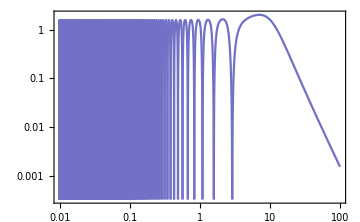

```mathematica
onecyl=LogLogPlot[(2π rho S1[1])/(P0cyn[1])//FullSimplify,{lam,0.01,100},PlotRange->{{0.01,100},{Automatic,Automatic}},Frame->True,FrameLabel->{MaTeX["\\lambda/R",Magnification->1.7],MaTeX["\\mathbb{P}/\\mathbb{P}_0",Magnification->1.7]},FrameStyle->Black,PlotStyle->niceblue,ImageSize->Medium,MaxRecursion->15](*plot for a single cylinder, takes few seconds because of the MaxRecursion*)
```

```mathematica
Export["power 1 cylinder.pdf",onecyl]
```

power 1 cylinder.pdf

### Many cylinders

```mathematica
n1=1.77; (*index of refraction*)
Clear[E0];(*induced electric field, total power will be normalized by E0, so the value does not matter*)
factor=E0*(1-1/n1^2); 
k=2π /lam; 
rho=110; (*radial distance of the point where the poyting vector is computed, integrated power is independent of this variable*)
lambda=logspace[-2,2,1000];(*numpy logspace*)
P0cyn[R1_]:=E0^2/2(1-1/n1^2)(1-1/n1)2π R1 ;
```

```mathematica
(*incoherent sum, takes few minutes*)
R=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.5]]],{i,1,500}];(*radius from a truncated gaussian of mean 1 and std 0.5*)
dataR=Total[S1[R]]/.lam->lambda;(*sum of the poynting vectors*)
```

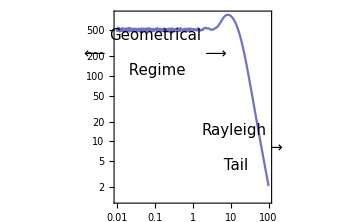

```mathematica
(*plotting incoherent sum*)
fivecyl=ListLogLogPlot[Table[{lambda[[i]]/Mean[R],(2π rho dataR[[i]])/(P0cyn[Mean[R]])},{i,1,Length[dataR]}],PlotRange->{{0.01,100},{Automatic,Automatic}},Frame->True ,FrameLabel->MaTeX[#&/@{"\\lambda/\\langle R\\rangle","P/\\mathbb{P}_0"},Magnification->1.7],FrameStyle->Black,PlotStyle->niceblue,Joined->True,ImageSize->Medium,Epilog->{Inset[Style["Geometrical\n⟵                     ⟶\n Regime",LineSpacing->{0,8},FontSize->15],{Log[0.10],Log[220]}],
Inset[Style["Rayleigh\n                   → \n Tail",LineSpacing->{0,8},FontSize->15],{Log[12],Log[8]}]}]
```

```mathematica
Export["power 500 cylinders.pdf",fivecyl]
```

power 500 cylinders.pdf

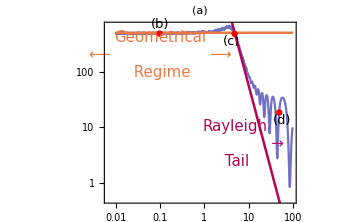

```mathematica
(*plotting python data. Filling factor=50% and std = 0.5*)
R=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.5]]],{i,1,2000}];(*radius from a truncated gaussian of mean 1 and std 0.5*)
E0=1; (*also normalized in the phyton code, ratio of the power should not depend on Subscript[E, 0]*)

(*plotting benchmark configuration filling factor=50%, σ=0.5⟨R⟩, ⟨R⟩=1, no loss*)
legend={Graphics[Text[Style["Geometrical\n⟵                     ⟶\n Regime",LineSpacing->{0,8},FontSize->15,niceorange],{Log[0.1],Log[200]}]],
Graphics[Text[Style["Rayleigh\n                   → \n Tail",LineSpacing->{0,8},FontSize->15,nicered],{Log[4.8],Log[5]}]],
Graphics[Text[Style["(b)",{FontColor->Black},FontSize->13],{Log[0.1],Log[700]}]],
Graphics[Text[Style["(c)",{FontColor->Black},FontSize->13],{Log[4],Log[350]}]],
Graphics[Text[Style["(d)",{FontColor->Black},FontSize->13],{Log[57],Log[13]}]]}; 

prolog={Opacity[0.2,niceorange],Rectangle[{Log[0.001],Log[0.1]},{Log[1],Log[1000]}], Opacity[0.2,nicered], Rectangle[{Log[π+2],Log[0.1]},{Log[100],Log[1000]}]
};
dataplot=Show[ListLogLogPlot[Table[{lambda[[i]]/Mean[R], fill5s5[[i]]/P0cyn[Mean[R]]},{i,1,Length[fill5s5]}],Joined->True,PlotStyle->niceblue,PlotRange->Automatic],
LogLogPlot[ factor^2/2(n1^4(2π/(lam/Mean[R]))^3 π^2)/4 Total[R^4] 1/P0cyn[Mean[R]] 1/150 ,{lam,0.5,55},PlotStyle->{nicered,Thickness[0.005]}],
LogLogPlot[500 ,{lam,0.01,100},PlotStyle->{niceorange,Thickness[0.005]}],ListLogLogPlot[{{lambda[[250]]/Mean[R],fill5s5[[250]]/P0cyn[Mean[R]]},{lambda[[673]]/Mean[R],fill5s5[[673]]/P0cyn[Mean[R]]},{lambda[[925]]/Mean[R],fill5s5[[925]]/P0cyn[Mean[R]]}},PlotStyle->Red],legend,
Frame->True,FrameLabel->MaTeX[#&/@{"\\lambda/\\langle R \\rangle","P/\\mathbb{P}_0"},Magnification->1.5],FrameStyle->Black,ImageSize->Medium,PlotLabel->Style["(a)",Black,FontSize->15]]
```

```mathematica
Export["fill5s5.pdf",dataplot]
```

fill5s5.pdf

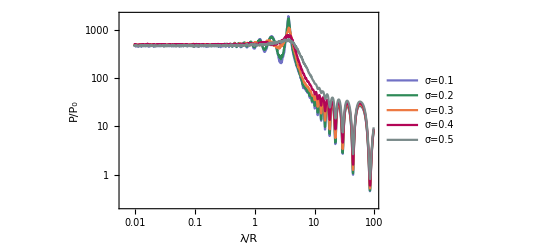

```mathematica
(*changing the standard deviation, P ∝ ⟨R^2⟩=σ^2+⟨R⟩^2*)
Rs1=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.1]]],{i,1,2000}];
Rs2=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.2]]],{i,1,2000}];
Rs3=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.3]]],{i,1,2000}];
Rs4=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.4]]],{i,1,2000}];
Rs5=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.5]]],{i,1,2000}];
ListLogLogPlot[{
Table[{lambda[[i]]/Mean[Rs5],Mean[Rs1^2]/Mean[Rs5^2] fill5s1[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[Rs5],Mean[Rs2^2]/Mean[Rs5^2] fill5s2[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[Rs5],Mean[Rs3^2]/Mean[Rs5^2] fill5s3[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[Rs5],Mean[Rs4^2]/Mean[Rs5^2] fill5s4[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[Rs5],Mean[Rs5^2]/Mean[Rs5^2] fill5s5[[i]]},{i,1,Length[fill1s5]}]
},Joined->True,PlotStyle->{niceblue,nicegreen,niceorange,nicered,lightcyan4},
PlotRange->Full,Frame->True,ImageSize->Full,FrameLabel->{Style["λ/R",FontSize->15,Black],Style["P/P_0",FontSize->15,Black]},FrameStyle->Black,
PlotLegends->Placed[LineLegend[{"σ=0.1","σ=0.2","σ=0.3","σ=0.4","σ=0.5"},LabelStyle->{FontSize->10},LegendFunction->(Framed[#1, FrameMargins -> 0] & ),LegendMarkerSize->12,Spacings->0.01],Scaled[{0.12,0.25}] ]]
```

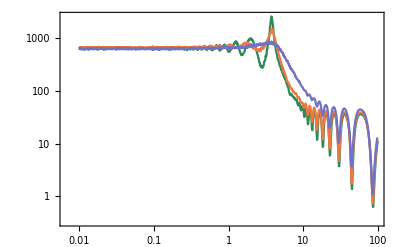

```mathematica
(*changing standard deviation normalized by Subscript[P, 0](⟨R⟩) times ⟨R^2⟩*)
E0=1;
(*lists for the reference power for each σ*)
Rs1=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.1]]],{i,1,2000}];
Rs3=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.3]]],{i,1,2000}];
Rs5=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.5]]],{i,1,2000}];
(*factor of 1.25 comes from σ=0.5⟨R⟩ as the reference σ^2+⟨R⟩^2=1.25⟨R⟩^2 *)
changstd=ListLogLogPlot[{
Table[{lambda[[i]]/Mean[Rs1],(Mean[Rs1]^2+(0.1 Mean[Rs1])^2)fill5s1[[i]]/P0cyn[Mean[Rs1]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[Rs3],(Mean[Rs3]^2+(0.3Mean[Rs3])^2)fill5s3[[i]]/P0cyn[Mean[Rs3]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[Rs5],(Mean[Rs5]^2+(0.5 Mean[Rs5])^2)fill5s5[[i]]/P0cyn[Mean[Rs5]]},{i,1,Length[fill1s5]}]
},Joined->True,PlotStyle->{nicegreen,niceorange,niceblue},
PlotRange->All,Frame->True,FrameLabel->MaTeX[#&/@{"\\lambda/\\langle R \\rangle","\\frac{\\langle R^2 \\rangle}{\\langle R^2 \\rangle|_{\\sigma=0.5}}\\frac{P}{\\mathbb{P}_0}"},Magnification->1.5],FrameStyle->Black,
PlotLegends->Placed[LineLegend[MaTeX[#&/@{"\\sigma_R=0.1\\langle R \\rangle","\\sigma_R=0.3\\langle R \\rangle","\\sigma_R=0.5\\langle R \\rangle"}],LabelStyle->{FontSize->10},LegendFunction->(Framed[#1, FrameMargins -> 0] & ),LegendMarkerSize->12,Spacings->0.01],Scaled[{0.20,0.25}] ],ImageSize->Full]
```

```mathematica
Rs1=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.1]]],{i,1,10000}];
Rs3=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.3]]],{i,1,10000}];
Rs5=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.5]]],{i,1,10000}];
Mean[Rs1^2]
(Mean[Rs1]^2+(0.1 Mean[Rs1])^2)
Mean[Rs3^2]
(Mean[Rs3]^2+(0.3 Mean[Rs3])^2)
Mean[Rs5^2]
(Mean[Rs5]^2+(0.5 Mean[Rs5])^2)
```

```mathematica
(*saving the plot range so all plots have the same*)
range=PlotRange[ListLogLogPlot[
Table[{lambda[[i]],1/1.25(1+0.1^2/Mean[Rs1]^2)fill5s1[[i]]/P0cyn[Mean[Rs1]]},{i,1,Length[fill1s5]}],PlotRange->Full]];
```

```mathematica
Export["changsigma.pdf",changstd]
```

changsigma.pdf

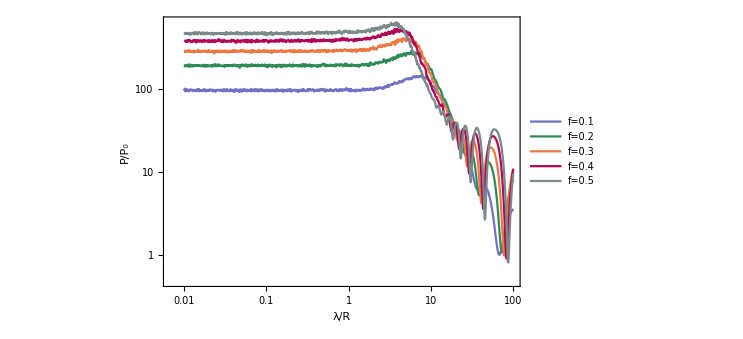

```mathematica
(*changing filling factor, P∝f*)
ListLogLogPlot[{
Table[{lambda[[i]],fill1s5[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]],fill2s5[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]],fill3s5[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]],fill4s5[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]],fill5s5[[i]]},{i,1,Length[fill1s5]}]
},Joined->True,PlotStyle->{niceblue,nicegreen,niceorange,nicered,lightcyan4},
PlotRange->All,Frame->True,FrameLabel->{Style["λ/R",FontSize->15,Black],Style["P/P_0",FontSize->15,Black]},FrameStyle->Black,
PlotLegends->Placed[LineLegend[{"f=0.1","f=0.2","f=0.3","f=0.4","f=0.5"},LabelStyle->{FontSize->10},LegendFunction->(Framed[#1, FrameMargins -> 0] & ),LegendMarkerSize->12,Spacings->0.01],Scaled[{0.12,0.25}] ]]
```

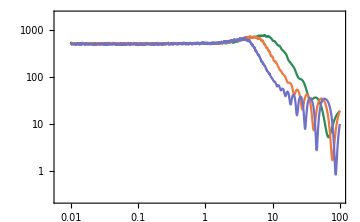

```mathematica
(*changing filling factor normalized*)
R=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.5]]],{i,1,2000}];
(*factor 0.5 comes from filling factor 50% being the reference*)
fillchang=ListLogLogPlot[{
Table[{lambda[[i]]/Mean[R],0.5/0.1 fill1s5[[i]]/P0cyn[Mean[R]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[R],0.5/0.3 fill3s5[[i]]/P0cyn[Mean[R]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[R],0.5/0.5 fill5s5[[i]]/P0cyn[Mean[R]]},{i,1,Length[fill1s5]}]
},Joined->True,PlotStyle->{nicegreen,niceorange,niceblue},
PlotRange->Exp[range],Frame->True,FrameLabel->MaTeX[#&/@{"\\lambda/\\langle R\\rangle","\\left(\\frac{0.5}{f}\\right) \\frac{P}{\\mathbb{P}_0}"},Magnification->1.5],FrameStyle->Black,
PlotLegends->Placed[LineLegend[MaTeX[#&/@{"f=0.1","f=0.3","f=0.5"}],LabelStyle->{FontSize->10},LegendFunction->(Framed[#1, FrameMargins -> 0] & ),LegendMarkerSize->12,Spacings->0.01],Scaled[{0.16,0.25}] ],ImageSize->Medium]
```

```mathematica
Export["changfill.pdf",fillchang]
```

changfill.pdf

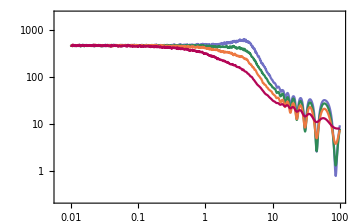

```mathematica
(*changing loss*)
changloss=ListLogLogPlot[{
Table[{lambda[[i]]/Mean[R],fill5s5[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[R],loss0p1[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[R],loss0p3[[i]]},{i,1,Length[fill1s5]}],
Table[{lambda[[i]]/Mean[R],loss1[[i]]},{i,1,Length[fill1s5]}]
},Joined->True,PlotStyle->{niceblue,nicegreen,niceorange,nicered,lightcyan4},
PlotRange->Exp[range],Frame->True,FrameLabel->MaTeX[#&/@{"\\lambda/\\langle R \\rangle","P/\\mathbb{P}_0"},Magnification->1.5],FrameStyle->Black,
PlotLegends->Placed[LineLegend[MaTeX[#&/@{"x_{\\rm cond}=0\\%","x_{\\rm cond}=0.1\\%","x_{\\rm cond}=0.3\\%","x_{\\rm cond}=1\\%"}],LabelStyle->{FontSize->10},LegendFunction->(Framed[#1, FrameMargins -> 0] & ),LegendMarkerSize->12,Spacings->0.01],Scaled[{0.19,0.28}] ],ImageSize->Medium]
```

```mathematica
Export["changloss.pdf",changloss]
```

changloss.pdf

## Spheres in 3D

### Single Sphere

```mathematica
n1=1.77; (*index of refraction*)
E0=1; (*axion electric field, total power will be normalized by E0, so value doesn't matter *)
factor=E0*(1-1/n1^2); (*for convenience*)
k=2π /lam; (*converted photon wave vector*)
rho=110; (*radial distance of the point where the poyting vector is computed, integrated power is independent of this variable*)
coeff[R_]:=(n1^2 k R SphericalBesselJ[1,n1 k R])/((SphericalHankelH1[1,k R])(D[x SphericalBesselJ[1,x],x]/.x->n1 k R)-n1^2 SphericalBesselJ[1,n1 k R]( D[x SphericalHankelH1[1,x],x]/.x-> R k)); (*"mie" coefficient*)
Espheric[R_]:= factor coeff[R] 1/(k rho)(D[r SphericalHankelH1[1, r],r]/.r->k rho); (* emitted electric field; should be times sinθ which is already integrated in the power*)
Bspheric[R_]:=  I factor coeff[R] SphericalHankelH1[1,k rho];(* emitted magnetic field; should be times sinθ which is already integrated in the power*)
Sspheric[R_]:=Re[1/2 Espheric[R]*Conjugate[Bspheric[R]]];(*Poynting vector emitted wave*)
Ssphericlarge[R_]:=E0^2/2((-1+n1^2)^2 R^6)/((2+n1^2)^2 rho^2)k^4;(*approxiamtion for λ>>R, corrected*)
Ssphericsmall[R_]:=E0^2/2 (1-1/n1^2)^2 R^2/(rho^2 (1+1/n1^2 Tan[k n1 R]^2));(*approximation for λ<<R, corrected*)
Pspheric[R_]:=(8π)/3 rho^2 Sspheric[R]; (*integral of poynting vector over angular region, integral of sin^3 θ is 4/3*)
P0sphere[R_]:=E0^2/2 (1-1/n1^2)(1-1/n1)8 π/3 R^2  (*choose R to be the √⟨R^2⟩ *)
```

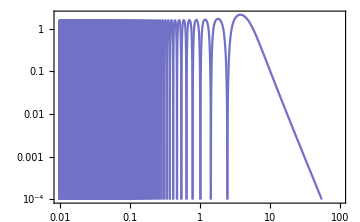

```mathematica
(*power single sphere, takes some time due to MaxRecursion*)
onesphere=LogLogPlot[(Pspheric[1])/(P0sphere[1]),{lam,0.01,100},PlotRange->{{0.01,100},{10^-4,Automatic}},Frame->True,FrameLabel->MaTeX[#&/@{"\\lambda/R","\\mathbb{P}/\\mathbb{P}_0"},Magnification->1.7],FrameStyle->Black,PlotStyle->niceblue,MaxRecursion->15,ImageSize->Medium]
```

```mathematica
Export["power 1 sphere.pdf",onesphere]
```

power 1 sphere.pdf

```mathematica
(*many spheres, incoherent sum*)
RF=Table[RandomVariate[TruncatedDistribution[{0,Infinity},NormalDistribution[1,0.5]]],{i,1,500}];(*radius chosen from truncated gaussian*)
dataF=Total[Sspheric[RF]]/.lam->logspace[-2,2,1000];(*sum of poynting vectors*)
```

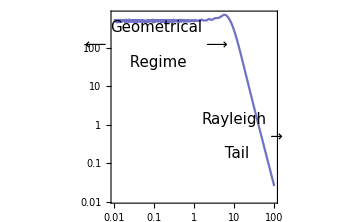

```mathematica
lambda=logspace[-2,2,1000];(*numpy logspace*)
fivespher=ListLogLogPlot[Table[{lambda[[i]],((8π)/3 rho^2 dataF[[i]])/(E0^2/2 (1-1/n1^2)(1-1/n1)8 π/3  Mean[RF^2] )},{i,1,Length[dataF]}],PlotRange->{{0.01,100},{Automatic,Automatic}},Frame->True,FrameLabel->MaTeX[#&/@{"\\lambda/\\langle R \\rangle","P/\\mathbb{P}_0"},Magnification->1.7],FrameStyle->Black,PlotStyle->niceblue,Joined->True,ImageSize->Medium,Epilog->{Inset[Style["Geometrical\n⟵                     ⟶\n Regime",LineSpacing->{0,8},FontSize->15],{Log[0.11],Log[120]}],
Inset[Style["Rayleigh\n                   → \n Tail",LineSpacing->{0,8},FontSize->15],{Log[10],Log[0.5]}]}]
```

```mathematica
Export["power 500 spheres.pdf",fivespher]
```

power 500 spheres.pdf

## 3D Reach Plots

### Plots for dp

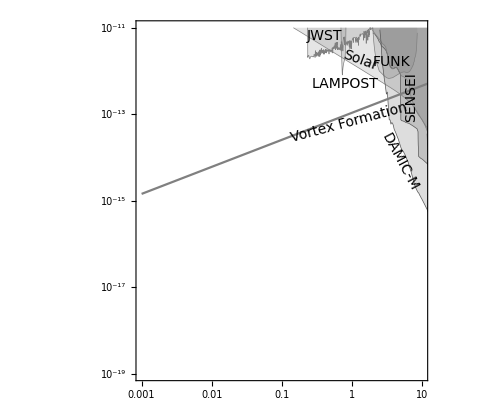

```mathematica
(*Current bounds*)
eV=1;(*everything will be measured in eV*)
topticks=Table[{2π/( 10^i μm),Superscript["10",i]},{i,-3,3}]; (*label for ticks at the top*)
bottomticks=Table[{10^i,Superscript["10",i]},{i,-3,3}];(*label for ticks at the bottom*)
unlabeledTicksTop=Flatten[Table[{k*j,Null},{k,9,2},{j,topticks[[All,1]]}],1];(*ticks at the top with no label*)
unlabeledTicksBottom=Flatten[Table[{k*j,Null},{k,2,9},{j,bottomticks[[All,1]]}],1];(*ticks at the bottom with no label*)
myTicksTop=Join[topticks,unlabeledTicksTop];(*join label and ticks*)
myTicksBottom=Join[bottomticks,unlabeledTicksBottom];(*join label and ticks*)

(*current bounds*)
boundsdp=Show[
ListLogLogPlot[{sensei1,damic,LAMPOST2022,darkside,cdms,jwst,funk1,xenonSolar,xenon1TSE,damicM}, 
Joined -> True,
 PlotRange -> {{10^-3,10^1}, {10^(-19),10^(-11)}},
FrameLabel -> { 
{MaTeX["\\varepsilon",Magnification->2],""},MaTeX[#&/@{"m_{A^\\prime}/\\text{eV}","\\lambda/\\mu\\text{m}"},Magnification->2]
},   
 Evaluate@plotstyle , 
FrameTicks->{
{Automatic,None},
{myTicksBottom,myTicksTop}},FrameTicksStyle->Directive[Black,20],
PlotStyle -> {
Directive[Darker[Gray],Thickness[0.001]],
Directive[Gray,Thickness[0.001]],
Directive[Gray,Thickness[0.001]],
Directive[Gray,Thickness[0.001]],
Directive[Gray,Thickness[0.001]],
Directive[Gray,Thickness[0.001]],
Directive[Gray,Thickness[0.001]],
Directive[Gray,Thickness[0.001]],
Directive[Gray,Thickness[0.001]]},
 Filling -> {1 -> Top, 2 -> Top,3-> Top, 4 -> Top, 5 -> Top,6->Top,7->Top,8->Top,9->Top,10->Top},
 Epilog -> {
tfn["LAMPOST",0.8,-12.3],
tfn[Rotate["SENSEI",π/2,Center],7,-12.6],
tfn[Rotate["DAMIC",π/2,Center],25,-13.3],
tfn["FUNK",3.7,-11.8],
tfn["",10,-14.6],
tfn[Rotate["Solar",-π/9,Center],1.3,-11.75],
tfn[Rotate["JWST",0,Center],0.4,-11.2],
tfn[Rotate["DarkSide",π/2,Center],37,-15],
tfn[Rotate["SuperCDMS",π/2,Center],50,-14.5],
	tfn["Haloscopes",10^-4,-12],tfn[Rotate["Vortex Formation",π/12,Center],10^-0.05,-13.2],,tfn[Rotate["DAMIC-M",-π/2.9,Center],10^0.68,-14.1]}],

ContourPlot[κ==(m/10^-6)^(5/8) 10^-14 1/(16 π^2)√((4π)/137),{m,10^-3,10^2},{κ,10^-18,10^-11},ScalingFunctions->{"Log","Log"},ContourStyle->Gray,PlotPoints->100](*vortex line*)
]
```

```mathematica
(*Definitions; hbar=1 so there is a 2pi between lambda and m*)
runtime=30*18*day; (*runtime of the experient 18 months*)
eff={0.85,0.5,0.5};(*detector efficiency for each band*)
la=1.6 meter ((2π/m )/(30 μm));(*absorption length as a funtion of λ/mass for Band C*)
FF=50/100;(*filling factor*)
n={1.7682,1.5599,3.377}; (*indices of refraction for all bands*)
V1={500 cm^3,5000 cm^3,(la  1)/(4  FF)cm^2}; (*effective volume for Phase 1;at band C: Subscript[V, eff]=(Subscript[A, sensor]*la)/(4*FF), Subscript[A, sensor]=1 cm^2 ; careful with units on the last entry*)
V2={5000 cm^3,50000 cm^3,(la  10)/(4  FF)cm^2}; (*effective volume for Phase 2; at band C: Subscript[V, eff]=(Subscript[A, sensor]*la)/(4*FF), Subscript[A, sensor]=10 cm^2 ; careful with units on the last entry*)
ρ=0.45 GeV/cm^3;(*local dm density*)
Events[Γdcr_,Γenv_,ef_,Tint_ ]:=Max[1.645 √(Tint (Γdcr+ef Γenv)),3]/Tint;(*1.645 comes from 2.7 σ, Subscript[Γ, dcr] is the background rate bellow*)
BGR1={10^-3 Hz,10^-2 Hz,10^-2 Hz}; (*background rate phase 1*)
BGR2={10^-6 Hz,10^-6 Hz,10^-6 Hz}; (*background rate phase 2*)
mmin={(2π)/(4μm),(2π)/(20μm),(2π)/(120μm)}; (*minimum mass for each band m=2π/λ*)
mmax={(2π)/(1μm),(2π)/(2μm),(2π)/(30μm)};(*maximum mass for each band m=2π/λ*)
mT[r_]:=(2π)/(3 r); (*trasition mass, need to choose. Choosing from comsol plot*)
stdR[r_]:=0.5 r (*standard deviation of the power, need to choose. Choosing benchmark value*)
Pdp[r_,V_]:= FF V (1-1/n^2)(1-1/n)2/3 κ^2 ρ 2(r^2+stdR[r]^2)/(r^3+3 r stdR[r]^2) ;(*dp power in the geometrical regime,P=V*FF*(1-1/n)(1-1/n^2)E0^2/2 (2⟨R^2⟩)/⟨R^3⟩, with E0^2/2=. For gaussian ⟨R^2⟩/⟨R^3⟩=(⟨R⟩^2+σ^2)/(⟨R⟩^3+3⟨R⟩σ^2) *)
(*power in the Rayleigh region is P=2 V*FF*((n^2-1)/(n^2+2))^2 2/3 κ^2 ρ ⟨R^6⟩/⟨R^3⟩((2π)/λ)^4 G . To find G we impose that the power of the geometrical and rayleigh match at m=mT*)
G3D[r_]:=((1-1/n^2)(1-1/n))/(((n^2-1)/(n^2+2))^2)(1/mT[r])^4((r^2+stdR[r]^2)/(r^6+15 r^4 stdR[r]^2+45 r^2 stdR[r]^4+15 stdR[r]^6));
(*power in the Rayleigh region*)
Prp[r_,m_,V_]:=G3D[r] 2 FF V ((n^2-1)/(n^2+2))^2 2/3 κ^2 ρ( m )^4((r^6+15 r^4 stdR[r]^2+45 r^2 stdR[r]^4+15 stdR[r]^6)/(r^3+3 r stdR[r]^2)); 

Fdp[r_,m_,V_]:=eff Pdp[r,V]/m//FullSimplify; (*photons per second = power reaching detector/ℏω, multiplied by efficiency == number of events, geometrical *)

Frp[r_,m_,V_]:=eff Prp[r,m,V]/m//FullSimplify;(*photons per second = power reaching detector/ℏω, multiplied by efficiency == number of events, Rayleigh *)
```

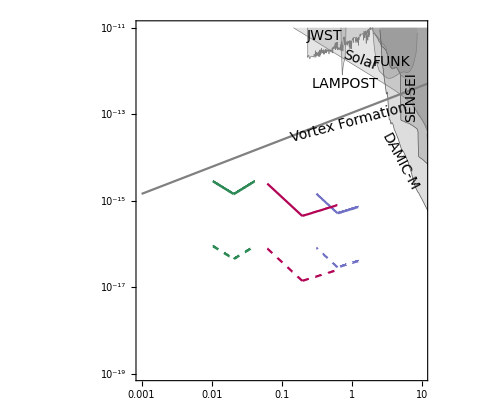

```mathematica
color={niceblue,nicered,nicegreen}; (*band colors*)
(*plots both phases for a given mean radius ⟨R⟩, and a given band num*)
plotp[r_,num_]:=Show[

(*Phase 1 not dashed*)
ContourPlot[Fdp[r, m,V1][[num]]==Events[BGR1[[num]],0,eff,runtime ],{m,mT[r],mmax[[num]]},{κ,10^-19,10^-11},ScalingFunctions->{"Log","Log"},ContourStyle->color[[num]],PlotPoints->100],
ContourPlot[Frp[r, m,V1][[num]]==Events[BGR1[[num]],0,eff,runtime ],{m,mmin[[num]],mT[r]},{κ,10^-19,10^-11},ScalingFunctions->{"Log","Log"},ContourStyle->color[[num]],PlotPoints->100],
(*Phase 2 dashed*)
ContourPlot[Fdp[r, m,V2][[num]]==Events[BGR2[[num]],0,eff,runtime ],{m,mT[r],mmax[[num]]},{κ,10^-19,10^-11},ScalingFunctions->{"Log","Log"},ContourStyle->{Dashed,color[[num]]},PlotPoints->100],
ContourPlot[Frp[r, m,V2][[num]]==Events[BGR2[[num]],0,eff,runtime ],{m,mmin[[num]],mT[r]},{κ,10^-19,10^-11},ScalingFunctions->{"Log","Log"},ContourStyle->{Dashed,color[[num]]},PlotPoints->100],PlotLabel->""];

(*choose ⟨R⟩ to be the geometric average of the bandwidth/3 and plots for all three bands*)
dp3Dplot=Show[boundsdp,plotp[GeometricMean[{1,4}]/3 μm,1],plotp[GeometricMean[{2,20}]/3 μm,2],plotp[GeometricMean[{30,120}]/3 μm,3]]
```

```mathematica
Export["reachplot_DP_3D.pdf",dp3Dplot]
```

reachplot_DP_3D.pdf

### Plots for axion

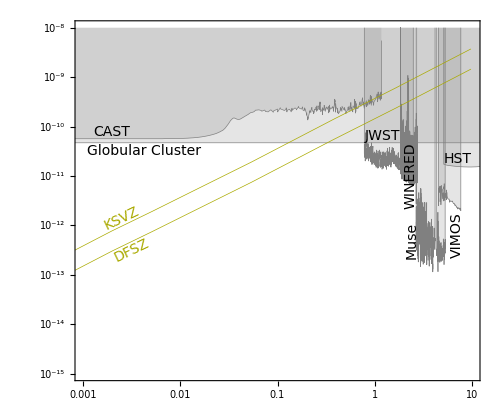

```mathematica
(*current bounds*)
eV=1;(*everything will be measured in eV*)
topticks=Table[{2π/(μm 10^i),Superscript["10",i]},{i,-3,3}];(*label for ticks at the top*)
bottomticks=Table[{10^i,Superscript["10",i]},{i,-3,3}];(*label for ticks at the bottom*)
unlabeledTicksTop=Flatten[Table[{k*j,Null},{k,10,9},{j,topticks[[All,1]]}],1];(*ticks at the top with no label*)
unlabeledTicksBottom=Flatten[Table[{k*j,Null},{k,2,9},{j,bottomticks[[All,1]]}],1];(*ticks at the bottom with no label*)
myTicksTop=Join[topticks,unlabeledTicksTop];(*join label and ticks*)
myTicksBottom=Join[bottomticks,unlabeledTicksBottom];(*join label and ticks*)

(*current bounds*)
boundsaxion=ListLogLogPlot[{AxionCast,AxionAstro,AxionHaloscope,AxionsHST,AxionsWINERED,AxionsMUSE,AxionsJWST,AxionsVIMOS,KSVZAxion,DFSZAxion}, 
Joined -> True,
 PlotRange -> { {10^-3,10^1}, {10^(-15),10^(-8)} },
FrameLabel -> { 
{MaTeX["g_{a\\gamma\\gamma}\\times\\text{GeV}",Magnification->2],""},MaTeX[#&/@{"m_a/\\text{eV}","\\lambda/\\mu\\text{m}"},Magnification->2]},   
 Evaluate@plotstyle , 
FrameTicks -> {{Automatic,None},{myTicksBottom,myTicksTop}},FrameTicksStyle->Directive[Black,20],
PlotStyle -> {
Directive[Full,Gray,Thickness[0.001]],
Directive[Full,Gray,Thickness[0.001]],
Directive[Full,Gray,Thickness[0.001]],
Directive[Full,Gray,Thickness[0.001]],
Directive[Full,Gray,Thickness[0.001]],
Directive[Full,Gray,Thickness[0.001]],
Directive[Full,Gray,Thickness[0.001]],
Directive[Full,Gray,Thickness[0.001]],
Directive[Darker[Yellow],Thickness[0.001]],
Directive[Darker[Yellow],Thickness[0.001]]
},
 Filling -> {1 -> Top, 2 -> Top,3->Top,4->Top,5->Top,6->Top,7->Top,8->Top,9->None,10->None},
 Epilog -> { tfn["CAST",10^-2.7,-10.1],tfn["Globular Cluster",10^-2.375,-10.5],tfn["JWST",1.2,-10.2],tfn[Rotate["WINERED",π/2,Center],2.3,-11],tfn["HST",7.1,-10.65],tfn[Rotate["Muse",π/2,Center],2.4,-12.3],tfn[Rotate["VIMOS",π/2,Center],7,-12.2],
tfn[Style[Rotate["DFSZ",π/7,{Center,Center}],Darker[Yellow]],10^-2.5,-12.5],
tfn[Style[Rotate["KSVZ",π/7,{Center,Center}],Darker[Yellow]],10^-2.6,-11.85]
}]
```

```mathematica
(*Definitions*)
(*Definitions; hbar=1 so there is a 2pi between lambda and m*)
runtime=30*18*day; (*runtime of the experient 18 months*)
eff={0.85,0.5,0.5};(*detector efficiency for each band*)
la=1.6 meter ((2π/m )/(30 μm));(*absorption length as a funtion of λ/mass for Band C*)
FF=50/100;(*filling factor*)
n={1.7682,1.5599,3.377}; (*indices of refraction for all bands*)
V1={500 cm^3,5000 cm^3,(la  1)/(4  FF)cm^2}; (*effective volume for Phase 1;at band C: Subscript[V, eff]=(Subscript[A, sensor]*la)/(4*FF), Subscript[A, sensor]=1 cm^2 ; careful with units on the last entry*)
V2={5000 cm^3,50000 cm^3,(la  10)/(4  FF)cm^2}; (*effective volume for Phase 2; at band C: Subscript[V, eff]=(Subscript[A, sensor]*la)/(4*FF), Subscript[A, sensor]=10 cm^2 ; careful with units on the last entry*)
ρ=0.45 GeV/cm^3;(*local dm density*)
Events[Γdcr_,Γenv_,ef_,Tint_ ]:=Max[1.645 √(Tint (Γdcr+ef Γenv)),3]/Tint;(*1.645 comes from 2.7 σ, Subscript[Γ, dcr] is the background rate bellow*)
BGR1={10^-3 Hz,10^-2 Hz,10^-2 Hz}; (*background rate phase 1*)
BGR2={10^-6 Hz,10^-6 Hz,10^-6 Hz}; (*background rate phase 2*)
mmin={(2π)/(4μm),(2π)/(20μm),(2π)/(120μm)}; (*minimum mass for each band m=2π/λ*)
mmax={(2π)/(1μm),(2π)/(2μm),(2π)/(30μm)};(*maximum mass for each band m=2π/λ*)
mT[r_]:=(2π)/(3 r); (*trasition mass, need to choose. Choosing from comsol plot*)
stdR[r_]:=0.5 r (*standard deviation of the power, need to choose. Choosing benchmark value*)
Pda[r_,m_,B_,V_]:=V FF (1-1/n)(1-1/n^2)(g 10^-9 B)^2 ρ/m^2 2(r^2+stdR[r]^2)/(r^3+3 r stdR[r]^2); (*axion power in the geometrical regime, P=V*FF*(1-1/n)(1-1/n^2)E0^2/2 (2⟨R^2⟩)/⟨R^3⟩, with E0^2/2=(g B)^2/m^2 ρ, 10^-9 comes because the coupling is in GeV. For gaussian ⟨R^2⟩/⟨R^3⟩=(⟨R⟩^2+σ^2)/(⟨R⟩^3+3⟨R⟩σ^2) *)

(*power in the Rayleigh region is P=2 V*FF*((n^2-1)/(n^2+2))^2 (g B)^2/m^2 ρ ⟨R^6⟩/⟨R^3⟩((2π)/λ)^4 G . To find G we impose that the power of the geometrical and rayleigh match at m=mT*)
G3D[r_]:=((1-1/n^2)(1-1/n))/(((n^2-1)/(n^2+2))^2)(1/mT[r])^4((r^2+stdR[r]^2)/(r^6+15 r^4 stdR[r]^2+45 r^2 stdR[r]^4+15 stdR[r]^6));
Pra[r_,m_,B_,V_]:=G3D[r] 2 V FF((n^2-1)/(n^2+2))^2(g 10^-9  B)^2 ρ ( m )^2 (r^6+15 r^4 stdR[r]^2+45 r^2 stdR[r]^4+15 stdR[r]^6)/(r^3+3 r stdR[r]^2); (*power in the Rayleigh region, m^2 comes from 1/m^2((2π)/λ)^4=m^4/m^2=m^2*)
Fda[r_,m_,B_,V_]:=eff Pda[r,m,B,V]/m//FullSimplify; (*photons per second = power reaching detector/ℏω, multiplied by efficiency == number of events, geometrical *)
Fra[r_,m_,B_,V_]:=eff Pra[r,m,B,V]/m//FullSimplify;(*photons per second = power reaching detector/ℏω, multiplied by efficiency == number of events, rayleigh *)
```

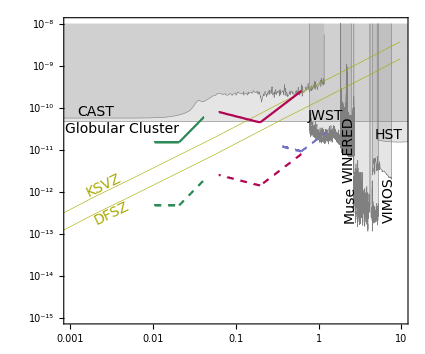

```mathematica
color={niceblue,nicered,nicegreen};(*color for bands*)
on={Opacity[0],Opacity[1],Opacity[1]}; (*not plotting the first phase of band A*)

(*plots phase 1 and 2 for a given mean radius and band. Taking magnetic field=10T*)
plota[r_,num_]:=Show[

(*phase 1 not dashed, opacity=0 for band A*)
ContourPlot[Fda[r, m,10Tesla,V1][[num]]==Events[BGR1[[num]],0,eff,runtime ],{m,mT[r],mmax[[num]]},{g,10^-16,10^-5},ScalingFunctions->{"Log","Log"},ContourStyle->{color[[num]],on[[num]]},PlotPoints->200],
ContourPlot[Fra[r, m,10Tesla,V1][[num]]==Events[BGR1[[num]],0,eff,runtime ],{m,mmin[[num]],mT[r]},{g,10^-16,10^-5},ScalingFunctions->{"Log","Log"},ContourStyle->{color[[num]],on[[num]]},PlotPoints->200],
(*phase 2 dashed*)
ContourPlot[Fda[r, m,10Tesla, V2][[num]]==Events[BGR2[[num]],0,eff,runtime ],{m,mT[r],mmax[[num]]},{g,10^-16,10^-5},ScalingFunctions->{"Log","Log"},ContourStyle->{Dashed,color[[num]]},PlotPoints->200],
ContourPlot[Fra[r, m,10Tesla, V2][[num]]==Events[BGR2[[num]],0,eff,runtime ],{m,mmin[[num]],mT[r]},{g,10^-16,10^-5},ScalingFunctions->{"Log","Log"},ContourStyle->{Dashed,color[[num]]},PlotPoints->200]]

(*choose ⟨R⟩ to be the geometric average of the bandwidth/3 and plots for all three bands*)
axion3Dplot=Show[boundsaxion,plota[GeometricMean[{1,4}]/3 μm,1],plota[GeometricMean[{2,20}]/3 μm,2],plota[GeometricMean[{30,120}]/3 μm,3]]
```

```mathematica
Export["reachplot_axion_3D.pdf",axion3Dplot]
```

reachplot_axion_3D.pdf